```mathematica
Clear["Global`*"]
```

```mathematica
pa={0,0};pb={Sqrt[3],0};pc={Sqrt[3]/2,3/2};
```

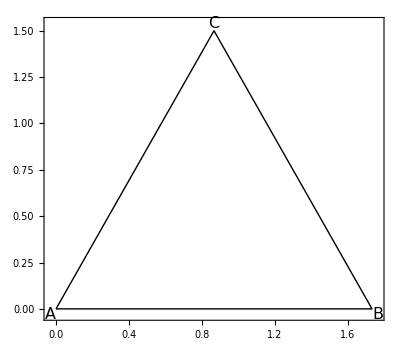

```mathematica
Graphics[{Line[{pa,pb,pc,pa}],Text[Style[A,16],pa+{-0.03,-0.03}],Text[Style[B,16],pb+{0.03,-0.03}],Text[Style[C,16],pc+{0,0.04}]},Frame->True]
```

```mathematica
t=Pi/3;r={{Cos[t],-Sin[t]},{Sin[t],Cos[t]}};
p={x,y};pp=r.p;
```

```mathematica
f1[x_,y_]:=1/2*Det[{{p[[1]],p[[2]],1},{pc[[1]],pc[[2]],1},{pp[[1]],pp[[2]],1}}];
```

```mathematica
a=Norm[p-pa];b=Norm[p-pb];c=Norm[p-pc];
f2[x_,y_]:=a+b+c;
```

```mathematica
area=Integrate[1,{x,0,Sqrt[3]/2},{y,0,Sqrt[3]/3*x}];
```

```mathematica
earea=Integrate[f1[x,y],{x,0,Sqrt[3]/2},{y,0,Sqrt[3]/3*x}]/area
```

(3 √3)/16

```mathematica
ecirc=Integrate[f2[x,y],{x,0,Sqrt[3]/2},{y,0,Sqrt[3]/3*x}]/area
```

1/4 √3 (4+Log[27])

```mathematica
N[earea,20]
N[ecirc,20]
```

0.32475952641916449254

3.1591900339133962422